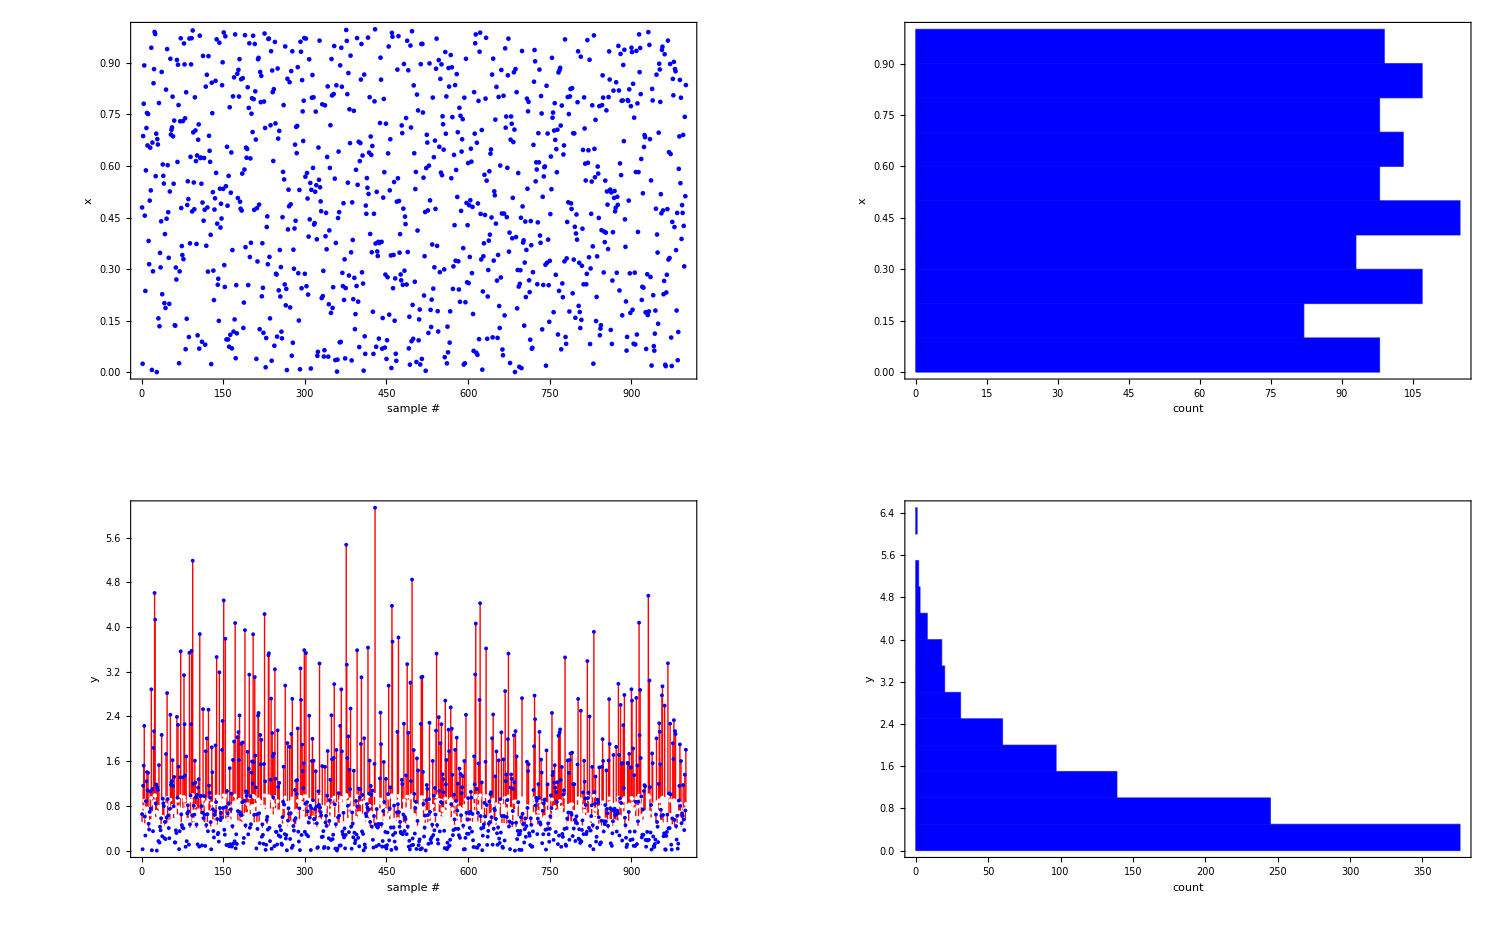

```mathematica
SetDirectory[NotebookDirectory[]];
n = 1000;
x=RandomReal[{0,1},n];
y=InverseCDF[ExponentialDistribution[1],x];
g1a=ListPlot[x,PlotStyle->Blue,PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"sample #","x"},BaseStyle->{FontSize->18}];
g2a=ListPlot[{x,y},PlotStyle->{White,Blue},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"sample #","y"},BaseStyle->{FontSize->18},Filling->{1->{2}},FillingStyle->Red];
g1b = Histogram[x,10,BarOrigin->Left,ChartStyle->Blue,PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"count","x"},BaseStyle->{FontSize->18}];
g2b = Histogram[y,10,BarOrigin->Left,ChartStyle->Blue,PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"count","y"},BaseStyle->{FontSize->18}];
gFinal=Show[GraphicsGrid[{{g1a,g1b},{g2a,g2b}}],ImageSize->1500]
```

```mathematica
Export["MCMC_inverseSamplingExponential.pdf",gFinal]
```

MCMC_inverseSamplingExponential.pdf